## Lab 3 Francesco Vassalli

#### Introduction

RC and LRC circuits are common tools for filtering specific frequencies of electronic signal by leveraging frequency dependent impedance.  We build, test, and characterize several RC/LRC circuits by demonstrating their gain relative to frequency. We predict and measure the cutoff frequency for low, high, and band pass filters.

### Experiment

We measure V_out wrt frequency for each circuit and compare the gain to prediction.

```mathematica
Grid[{{"Component name","Spec","Measured","Uncertainty"},{"R1","10kΩ","9.91 kΩ",".09"},{"R2","6.8kΩ","6.75 kΩ",".06"},{"R3","10kΩ","9.94 kΩ",".09"},{"R4","10kΩ","9.83 kΩ",".09"},{"R5","10kΩ","9.987kΩ",".09"},{"C1","1nF","1 nF",".012"},{"C2","1nF","1 nF",".012"},{"C3","10nF","10 nF",".12"},{"L","10mH","10.06",".01"}},Frame->All]
```

Component name | Spec | Measured | Uncertainty
R1 | 10kΩ | 9.91 kΩ | .09
R2 | 6.8kΩ | 6.75 kΩ | .06
R3 | 10kΩ | 9.94 kΩ | .09
R4 | 10kΩ | 9.83 kΩ | .09
R5 | 10kΩ | 9.987kΩ | .09
C1 | 1nF | 1 nF | .012
C2 | 1nF | 1 nF | .012
C3 | 10nF | 10 nF | .12
L | 10mH | 10.06 | .01

Table of all the components used in this lab.

Schematic of the voltage divider

Schematic of the low pass filter

Schematic of the high pass filter

Schematic of the band filter

attenuation=gain*V_in=R2/(R1+R2)

f_(3dB)=(ω_(3dB))/(2π)=(2πRC)^-1

f_0=(2πLC)^-1

Q=f_0/(f_(3dB))

```mathematica
Grid[{{"Voltage Divider","attenuation=.41V"},{"Low Pass","f_(3  dB)=16±.2kHz"},{"High Pass","f_(3  dB)=16±.2kHz"},{"Band","f_0=15.87kHz, Q=9.84"}},Frame->All]
```

Voltage Divider | attenuation=.41V
Low Pass | f_(3  dB)=16±.2kHz
High Pass | f_(3  dB)=16±.2kHz
Band | f_0=15.87kHz, Q=9.84

Predicted values for the circuits using equations 1-4.

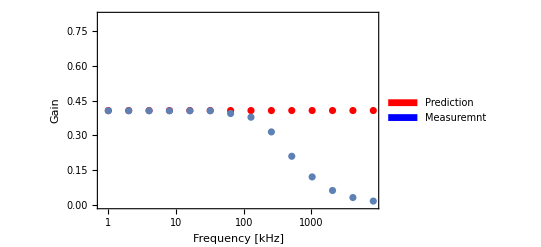

```mathematica
measuredGain=measuredVpp/1010;
predictedGain=Table[.407,{i,14}];
predictedGainError=Table[ErrorBar[.004],{i,14}];
mGainPlot=ListPlot[Thread[{f,measuredGain}],ScalingFunctions->{"Log"}];
pGainPlot=ErrorListPlot[Thread[{Thread[{f,predictedGain}],predictedGainError}],ScalingFunctions->{"Log"},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency [kHz]", "Gain"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},
PlotLegends->SwatchLegend[{Red,Blue},{"Prediction","Measuremnt"}]
];
Show[pGainPlot,mGainPlot]
```

The predicted and measured gain of the voltage divider using the coax cables.

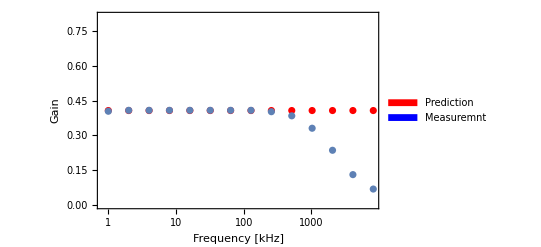

```mathematica
measuredVpp={408,412,412,412,412,412,412,412,406,388,334,238,132,69.2};
measuredGain=measuredVpp/1010;
predictedGain=Table[.407,{i,14}];
predictedGainError=Table[ErrorBar[.004],{i,14}];
mGainPlot=ListPlot[Thread[{f,measuredGain}],ScalingFunctions->{"Log"}];
pGainPlot=ErrorListPlot[Thread[{Thread[{f,predictedGain}],predictedGainError}],ScalingFunctions->{"Log"},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency [kHz]", "Gain"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},
PlotLegends->SwatchLegend[{Red,Blue},{"Prediction","Measuremnt"}]
];
Show[pGainPlot,mGainPlot]
```

The predicted and measured gain of the voltage divider using the scope probe.

Reducing capacitance in our measurement system shows the data agrees for a much higher range.

```mathematica
Grid[{{"Measurement","Cutoff f","deviation from expection [σ]"},{"Coax divider","320 kHz"},{"Scope Probe divider","1.442 MHz"},{"Low Pass","16.65 kHz","2"},{"High Pass","16.00 kHz","<1"}},Frame->All]
```

Measurement | Cutoff f | deviation from expection [σ]
Coax divider | 320 kHz | 
Scope Probe divider | 1.442 MHz | 
Low Pass | 16.65 kHz | 2
High Pass | 16.00 kHz | <1

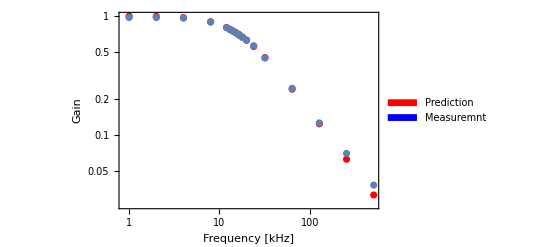

```mathematica
f={1,2,4,8,12,13,14,15,16,16.65,18,20,24,32,64,128,256,512};
measuredVpp={1,1,.988,.916,.824,.792,.768,.748,.728,.708,.680,.648,.580,.456,.254,.130,.072,.039};
measuredGain=measuredVpp/1.03;
lowGain[ω_,res_,cap_]:=Abs[1/(1+ⅈ*ω*cap*res)];
R3=9.94*10^3;
C1=10^-9;
predictedGain=Table[lowGain[Part[f,i]*10^3*2*π,R3,C1],{i,18}];
pGainPlot=ListPlot[Thread[{f,predictedGain}],ScalingFunctions->{"Log","Log"},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency [kHz]", "Gain"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},
PlotLegends->SwatchLegend[{Red,Blue},{"Prediction","Measuremnt"}]];
mGainPlot=ListPlot[Thread[{f,measuredGain}],ScalingFunctions->{"Log","Log"}];
Show[pGainPlot,mGainPlot]
```

The predicted and measured gain of the low pass filter using the scope probe.

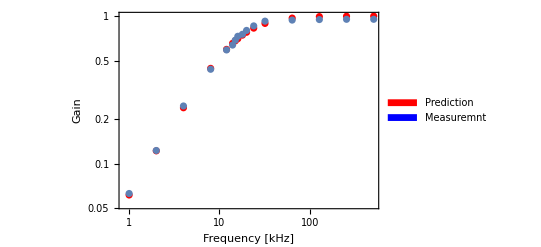

```mathematica
f={1,2,4,8,12,14,15,16,18,20,24,32,64,128,256,512};
measuredVpp={.065,.127,.254,.450,.608,.656,.708,.752,.776,.824,.884,.952,.968,.976,.980,.980};
measuredGain=measuredVpp/1.03;
highGain[ω_,res_,cap_]:=Abs[res/((ⅈ*ω*cap)^-1+res)];
R4=9.83*10^3;
C2=10^-9;
predictedGain=Table[highGain[Part[f,i]*10^3*2*π,R4,C2],{i,16}];
pGainPlot=ListPlot[Thread[{f,predictedGain}],ScalingFunctions->{"Log","Log"},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency [kHz]", "Gain"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},
PlotLegends->SwatchLegend[{Red,Blue},{"Prediction","Measuremnt"}]];
mGainPlot=ListPlot[Thread[{f,measuredGain}],ScalingFunctions->{"Log","Log"}];
Show[pGainPlot,mGainPlot]
```

The predicted and measured gain of the high pass filter using the scope probe.

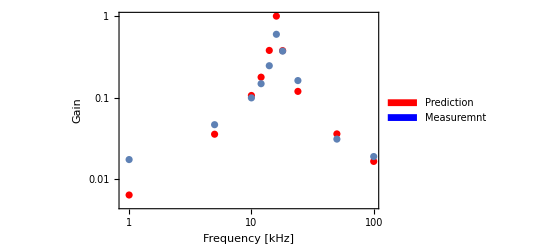

```mathematica
bandgain[ω_,r_,c_,l_]:=Abs[((ⅉ*ω*c)^-1+ⅉ*ω*l)^-1/(((ⅉ*ω*c)^-1+ⅉ*ω*l)^-1+r)];
f={1,5,10,12,14,16,18,24,50,100};
measuredVpp={.018,.048,.102,.152,.252,.610,.380,.166,.032,.0196};
measuredGain=measuredVpp/1.03;
R5=9.837*10^3;
C3=10^-8;
L=10.06*10^-3;
zeff[ω_,l_,C_]:=ⅉ*ω*L*(1-ω^2*L*C)^-1;
h[ω_,r_,c_,l_]:=Abs[zeff[ω,l,c]/(zeff[ω,l,c]+r)];
predictedGain=Table[h[Part[f,i]*10^3*2*π,R5,C3,L],{i,10}];
pGainPlot=ListPlot[Thread[{f,predictedGain}],ScalingFunctions->{"Log","Log"},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency [kHz]", "Gain"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},
PlotLegends->SwatchLegend[{Red,Blue},{"Prediction","Measuremnt"}]];
mGainPlot=ListPlot[Thread[{f,measuredGain}],ScalingFunctions->{"Log","Log"}];
Show[pGainPlot,mGainPlot]
```

The predicted and measured gain of the band pass filter using the scope probe.

We measured f_0 of the band pass circuit by maximizing the amplitude, and by matching the phase of the input and output.  Maximizing the amplitude is more precise.

```mathematica
Grid[{{"Max amp",".890V","17.17±.01 kHz"},{"phase match",".870V","17.09±.07 kHz"}},Frame->All]
```

Max amp | .890V | 17.17±.01 kHz
phase match | .870V | 17.09±.07 kHz

These measurements do not agree with the prediction.  I speculate that unaccounted differences between the frequency the inductance was measured at and the resonance frequency contribute to the error.  Using equation 3 the inductance of 8.6mH can be derived from these measurements.  This inductance is significantly different.  The measured quality is 7.465 which is significantly less than the predicted quality.  This discrepancy is a common phenomena of unideal circuits.  This can be partially corrected by accounting for the series resistance of the inductor.

Q_refined=(R/R_L)/(R √(C/L)+R_L^-1 √(L/C))

This refinement yields a new predicted Q of 9.28 which still disagrees with our measured value.

### Summary

We created several filters and compared measured and predicted gain.  These comparisons agree for the low and high pass indicating the circuits are well constructed.  The band pass filter has lower than predicted quality and higher than predicted resonant frequency likely due to loss of inductance around the resonance point.

### Auxiliary Plots

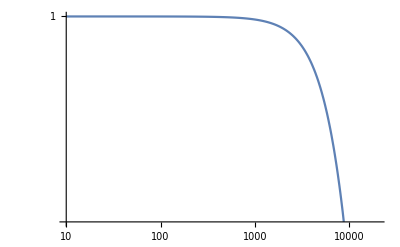

```mathematica
LogLogPlot[lowGain[ff*2*π,R3,C1],{ff,10,20000}]
```

Low Pass Prediction.

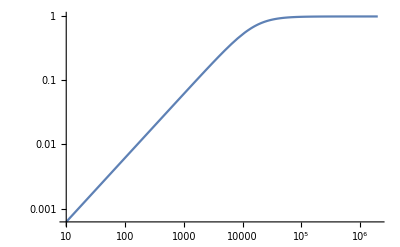

```mathematica
LogLogPlot[highGain[ff*2*π,R4,C2],{ff,10,2000000}]
```

High Pass Prediction.